```mathematica
fs[n_,k_,s_] := Expand[(-1)^(k)((1/(1-s))^(k)-n^(1-s)/(1-s) Sum[1 /j!(-Log[n])^j  (1/(1-s))^(k-j-1), {j,0,k-1}])]
Fa4[n_,a_,s_]:=(-1)^a Integrate[t^(a-1)E^(-(1-s) t),{t,0,-Log[n]}]/Gamma[a]
Fa5[n_,a_,s_]:=(-1)^a((Integrate[Log[t^-1]^(a-1),{t,1/(n^(s-1)),1}]) (1-s)^-a)/Integrate[Log[t^-1]^(a-1),{t,0,1}]
Fa3[n_,a_,s_]:=(-1)^a((Gamma[a,0,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
```

```mathematica
N[{Fa4[100,ac=2,ca=-1],Fa5[100,ac,ca],Fa3[100,ac,ca],fs[100,ac,ca]}]
```

{20526.1,20526.1,20526.1-2.51369×10^-12 ⅈ,20526.1}

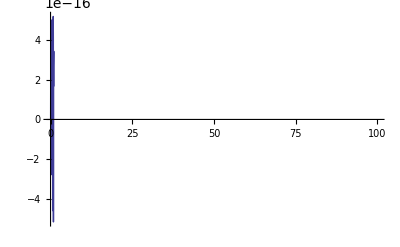

```mathematica
Plot[fs[n,cc=2,dc=1/2]-Fa3[n,cc,dc],{n,0,100}]
```

```mathematica
Limit[(Fa3[n,a,s]-1)/a,{a->0}]
```

{ⅈ π-Gamma[0,(-1+s) Log[n]]-Log[1-s]}

```mathematica
cc[n_,s_]:=-ⅈ π-Gamma[0,(-1+s) Log[n]]-Log[1-s]
```

```mathematica
N[cc[100,-1]]
```

1245.44+0. ⅈ

```mathematica
cd[n_,s_]:=-ⅈ π-Gamma[0, Log[n^(-1+s)]]-Log[1-s]
```

```mathematica
N[cd[100,-1]]
```

1245.44+0. ⅈ

```mathematica
N[ExpIntegralEi[Log[100]]]
```

30.1261

```mathematica
N[ExpIntegralEi[Log[100^2]]]
```

1246.14

```mathematica
N[LogIntegral[100]]
```

30.1261

```mathematica
N[LogIntegral[10000]]-Log[2]
```

1245.44

```mathematica
N[cc[100,2]]
```

-0.00182974-6.28319 ⅈ

```mathematica
N[LogIntegral[100^-1]]
```

-0.00182974

```mathematica
N[cc[100,3]]
```

-0.693157-6.28319 ⅈ

```mathematica
N[LogIntegral[100^-2]]-Log[2]
```

-0.693157

```mathematica
cc[100,-1]
```

-ⅈ π-Gamma[0,-2 Log[100]]-Log[2]

```mathematica
jj[n_,s_] := Sum[ N[MangoldtLambda[j]/Log[j]] j^-s,{j,2,n}]
```

```mathematica
jj[100,-1]
```

1156.48

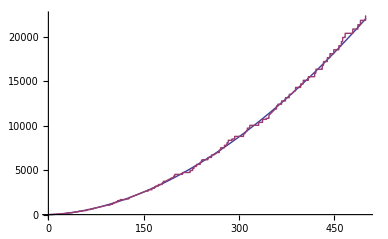

```mathematica
Plot[{ Re[ -ⅈ π-Gamma[0,-2 Log[n]]-Log[2]], jj[Floor[n],-1]},{n,1,500}]
```

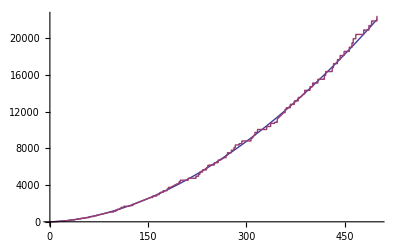

```mathematica
Plot[{ Re[ cc[n,s2=-1]], jj[Floor[n],s2]},{n,1,500}]
```

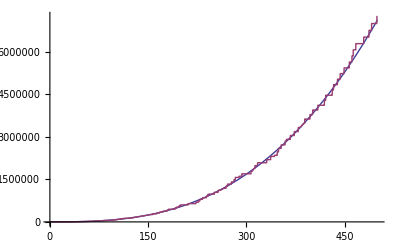

```mathematica
Plot[{ Re[ cc[n,s2=-2]], jj[Floor[n],s2]},{n,1,500}]
```

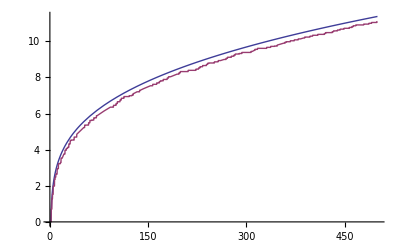

```mathematica
Plot[{ Re[ cc[n,s2=1/2]], jj[Floor[n],s2]},{n,1,500}]
```

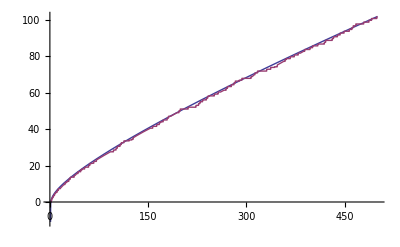

```mathematica
Plot[{ Re[ cc[n,s2=0]], jj[Floor[n],s2]},{n,1,500}]
```

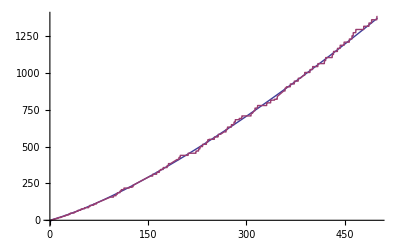

```mathematica
Plot[{ Re[ cc[n,s2=-1/2]], jj[Floor[n],s2]},{n,1,500}]
```

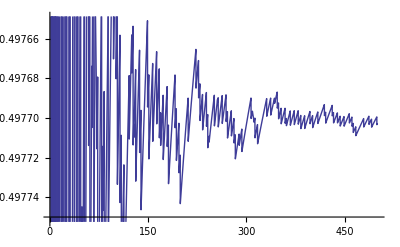

```mathematica
Plot[{ Re[ cc[n,s2=2]] - jj[Floor[n],s2]},{n,1,500}]
```

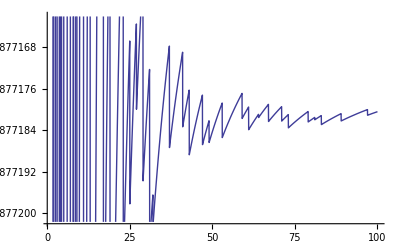

```mathematica
Plot[{ Re[ cc[n,s2=3]] - jj[Floor[n],s2]},{n,1,100}]
```

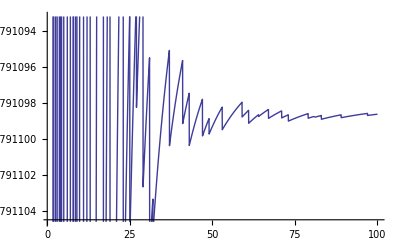

```mathematica
Plot[{ Re[ ce[n,s2=4]] - jj[Floor[n],s2]},{n,1,100}]
```

```mathematica
cc[n,4]
```

-2 ⅈ π-Gamma[0,3 Log[n]]-Log[3]

```mathematica
N[Log[3]]
```

1.09861

```mathematica
ce[n_,s_]:=-Gamma[0,(s-1) Log[n]]
```

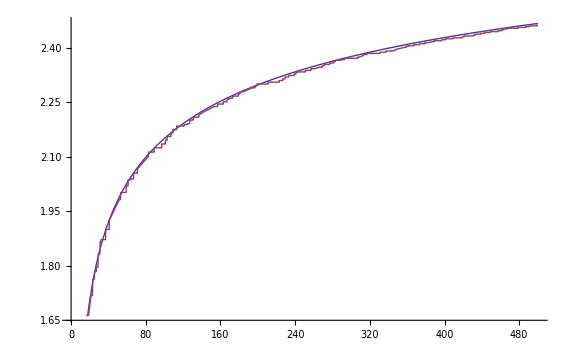

```mathematica
Plot[{ Re[ cc[n,s2=.99]], jj[Floor[n],s2]},{n,1,500}]
```

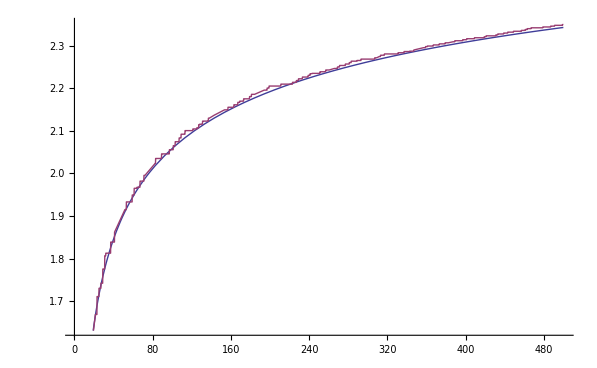

```mathematica
Plot[{ Re[ cc[n,s2=1.01]], jj[Floor[n],s2]},{n,1,500}]
```

```mathematica
dif[n_,s_, t_]:=((cc[n+t,s])-(cc[n-t,s]))/(2t)
```

```mathematica
se[n_,a_,s_] := Sum[ ((a^(1-s))^k-1)/k,{k,1,Log[a,n]}]
```

```mathematica
se[100,1.00001,0]
```

28.0218

```mathematica
N[LogIntegral[100]]-EulerGamma-Log[Log[100]]
```

28.0217

```mathematica
se[100,1.00001,-1]
```

1243.34

```mathematica
N[LogIntegral[10000]]-EulerGamma-Log[Log[10000]]
```

1243.34

```mathematica
se[100,1.000001,-2]
```

78624.5+1.27973×10^-9 ⅈ

```mathematica
N[LogIntegral[1000000]]-EulerGamma-Log[Log[1000000]]
```

78624.3

4.75435

```mathematica
s=1/2;{se[100,1.00001,(1-s)],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{4.75435,4.75435}

```mathematica
s=1;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

Infinity::indet: Indeterminate expression -EulerGamma + -∞ + ∞ encountered.

{0.,Indeterminate}

```mathematica
s=0;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{28.0218,28.0217}

```mathematica
s=-1;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{1243.34,1243.34}

```mathematica
s=2;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{-2.10622,-2.10623-3.14159 ⅈ}

```mathematica
s=3;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{-2.79754,-2.79755-3.14159 ⅈ}

```mathematica
s=2.5;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]]}
```

{-2.50998,-2.50999-3.14159 ⅈ}

```mathematica
s=1/2+I;{se[100,1.00001,s]+EulerGamma+Log[(1-s)Log[100]],N[LogIntegral[100^(1-s)]]-EulerGamma-Log[Log[100^(1-s)]],N[ExpIntegralEi[(1-s)Log[100]]]}
```

{-1.98461-2.81852 ⅈ,1.54732+5.09858 ⅈ,-1.98461-2.81853 ⅈ}

```mathematica
s=2;{se[100,1.00001,s],N[LogIntegral[100^(1-s)]],N[ExpIntegralEi[(1-s)Log[100]]],N[ExpIntegralEi[Log[100^(1-s)]]]}
```

{-2.10622,-0.00182974,-0.00182974,-0.00182974}

```mathematica
s=N[ZetaZero[4]];{se[nn=1200,1.00001,s]+EulerGamma+Log[(1-s)Log[nn]],N[ExpIntegralEi[(1-s)Log[nn]]],-Gamma[0,-(1-s)Log[nn]]}
```

{0.138743-3.22227 ⅈ,0.138753-3.22241 ⅈ,0.138753-0.0808157 ⅈ}

```mathematica
se2[a_,s_,k_] :=  ((a^(1-s))^k-1)/k
```

```mathematica
Sum[ N[se2[1.0001,ZetaZero[a],1]+se2[1.0001,ZetaZero[-a],1]],{a,1,5000}]
```

-543.018+0. ⅈ

```mathematica
Sum[ N[se2[1.0001,ZetaZero[a],2]+se2[1.0001,ZetaZero[-a],2]],{a,1,5000}]
```

-1038.19+0. ⅈ

```mathematica
Sum[ N[se2[1.0001,ZetaZero[a],3]+se2[1.0001,ZetaZero[-a],3]],{a,1,5000}]
```

-1443.36+0. ⅈ

```mathematica
Sum[ N[se2[1.0001,ZetaZero[a],4]+se2[1.0001,ZetaZero[-a],4]],{a,1,5000}]
```

-1729.2+0. ⅈ

```mathematica
sse[n_,a_,s_]:= se[n,a,s]+EulerGamma+Log[(1-s)Log[n]]
```

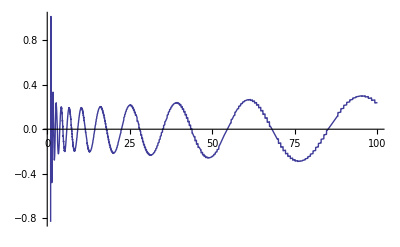

```mathematica
Plot[Re[sse[n,aa=1.01,N[ZetaZero[1]]]+sse[n,aa,N[ZetaZero[-1]]]],{n,1,100}]
```

```mathematica
Re[sse[n,2,N[ZetaZero[1]]]+sse[n,2,N[ZetaZero[-1]]]]/.{n->6}
```

Re[sse[6,2,0.5-14.1347 ⅈ]+sse[6,2,0.5+14.1347 ⅈ]]

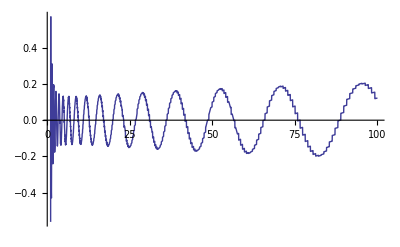

```mathematica
Plot[Re[sse[n,aa=1.01,N[ZetaZero[2]]]+sse[n,aa,N[ZetaZero[-2]]]],{n,1,100}]
```

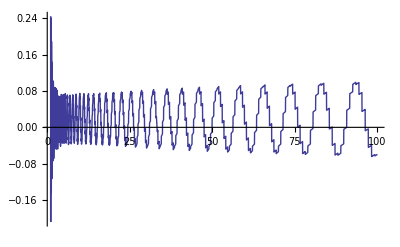

```mathematica
Plot[Re[sse[n,aa=1.01,N[ZetaZero[11]]]+sse[n,aa,N[ZetaZero[-11]]]],{n,1,100}]
```

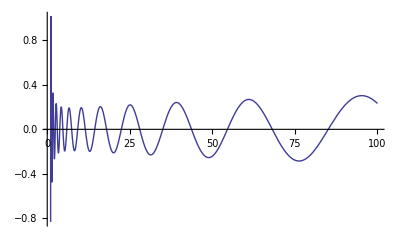

```mathematica
Plot[Re[-Gamma[0,-(1-ZetaZero[tt=1])Log[n]]-Gamma[0,-(1-ZetaZero[-tt])Log[n]]],{n,1,100}]
```

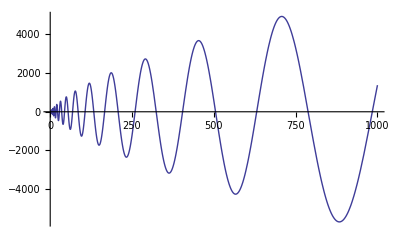

```mathematica
Plot[Re[-Gamma[pa=2,-(1-ZetaZero[tt=1])Log[n]]-Gamma[pa,-(1-ZetaZero[-tt])Log[n]]],{n,1,1000}]
```

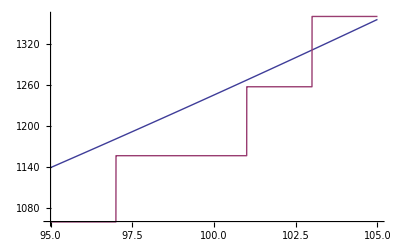

```mathematica
Plot[{ Re[ cc[n,s2=-1]], jj[Floor[n],s2]},{n,95,105}]
```

```mathematica
Integrate[ x^(s-1)/(E^x-1),{x,0,Infinity}]
```

ConditionalExpression[Gamma[s] PolyLog[s,1],Re[s]>1]

```mathematica
ts[n_, s_]:=Integrate[ t^(s-1)/(E^t-1),{t,0,Infinity}]/Gamma[s]
ts4[n_, k_,s_]:=Integrate[ t^(s-1)/((E^((1-k)t)-1)),{t,0,Infinity}]/Gamma[s]
eta[n_, k_,s_]:=Integrate[ t^(s-1)/((E^((1-k)t)+1)),{t,0,Infinity}]/Gamma[s]
```

```mathematica
Fa4[n_,k_,s_]:=(-1)^k Integrate[t^(k-1)E^(-(1-s) t),{t,0,-Log[n]}]/Gamma[k]
Fa3[n_,k_,s_]:=(-1)^k((Gamma[k,0,-(1-s) Log[n]]) (1-s)^-k)/Gamma[k]
Fa32[n_,k_,s_]:=(-1)^k((Gamma[k]-Gamma[k,-(1-s) Log[n]]) (1-s)^-k)/Gamma[k]
```

```mathematica
ts[100,2]
```

π^2/6

```mathematica
ts4[100,-1,2]
```

π^2/24

```mathematica
eta[100,-1,2]
```

π^2/48

```mathematica
Gamma[1-z]Gamma[z]
```

Gamma[1-z] Gamma[z]

```mathematica
N[Fa3[100,2,2]]
```

0.943948

```mathematica
Fa32[100,2,-1]
```

1/4 (1-Gamma[2,-2 Log[100]])

```mathematica
Integrate[ 1, {j,1,n},{k,1,n/j},{m,1,n/(j k)}]
```

ConditionalExpression[-1+n+1/2 n (-2+Log[n]) Log[n],Re[n]≥0||n∉Reals]

```mathematica
Integrate[ j^-s k^-s m^-s, {j,1,n},{k,1,n/j},{m,1,n/(j k)}]
```

```mathematica
Expand[ConditionalExpression[(n^-s (2 n^s+n (-2+(-1+s) Log[n] (-2+Log[n]-s Log[n]))))/(2 (-1+s)^3),Re[n]≥0||n∉Reals]]
```

ConditionalExpression[1/(-1+s)^3-n^(1-s)/(-1+s)^3+(n^(1-s) Log[n])/(-1+s)^3-(n^(1-s) s Log[n])/(-1+s)^3-(n^(1-s) Log[n]^2)/(2 (-1+s)^3)+(n^(1-s) s Log[n]^2)/(-1+s)^3-(n^(1-s) s^2 Log[n]^2)/(2 (-1+s)^3),Re[n]≥0||n∉Reals]

```mathematica
fo[n_]:=-1+n+1/2 n (-2+Log[n]) Log[n]
```

```mathematica
fo2[n_]:=Fa3[n,3,0]
```

```mathematica
N[fo[100]]
```

698.863

```mathematica
N[fo2[100]]
```

698.863-1.71417×10^-13 ⅈ

```mathematica
Fa32[n_,a_,s_]:=(-1)^a((Gamma[a,-(1-s) Log[n]]) (1-s)^-a)/Gamma[a]
```

```mathematica
fo3[n_]:=1/2 n (2 (-1+n) n-Log[n] (2 n+Log[n]))
```

```mathematica
fo4[n_]:=Fa32[n,3,0]
```

```mathematica
N[fo3[100]]
```

942888.

```mathematica
N[fo4[100]]
```

-699.863+1.71417×10^-13 ⅈ

```mathematica
Gamma[1,0,-Log[n]]
```

1-n

```mathematica
Gamma[1,-Log[n]]
```

n

```mathematica
Gamma[2,0,-Log[n]]
```

Gamma[2,0,-Log[n]]

```mathematica
Gamma[2,-Log[n]]
```

Gamma[2,-Log[n]]

```mathematica
Limit[(Gamma[a,0,-Log[n]]/Gamma[a]-1)/a,{a->0}]
```

{-Gamma[0,-Log[n]]}

```mathematica
Limit[(Gamma[a,0,-Log[n]]/Gamma[a]-1)/a,{a->4}]
```

{-1/24 Gamma[4,-Log[n]]}